### Option pricing functions - Normal - definitions

```mathematica
nn[x_,μ_:0,σ_:1]:=(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ);
NN[x_,μ_:0,σ_:1]:=1/2 Erfc[(-x+μ)/(√2 σ)];
NNInv[y_,μ_:0,σ_:1]:=μ-√2 σ InverseErfc[2 y];
```

```mathematica
Solve[NN[x,μ,σ]==y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→μ-√2 σ InverseErfc[2 y]}}

#### Option pricing functions - Normal - expected behavior

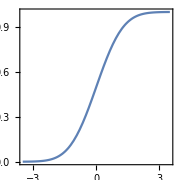

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-3.5,+3.5},AspectRatio->1,Frame->True,AxesOrigin->{0,1/2},ImageSize->Small]
```

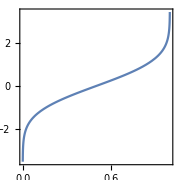

```mathematica
Plot[-√2  InverseErfc[2 y],{y,0,1},AspectRatio->1,Frame->True,AxesOrigin->{1/2,0},ImageSize->Small]
```

```mathematica
{nn[-∞]==0,nn[+∞]==0,NN[-∞]==0,NN[+∞]==1}
```

{True,True,True,True}

### Option pricing functions - d1, d2 - definitions

```mathematica
dd1[x_,K_,σ_,τ_]:=If[τ==0,If[x==K,0,Sign[Log[x/K]]Infinity],(Log[x/K]+(σ^2τ)/2)/(σ Sqrt[τ])];
dd1::usage="dd1[x,K,σ,τ] returns d1 for the price x, the strike K, volatility σ and time to expiry τ";
dd2[x_,K_,σ_,τ_]:=If[τ==0,If[x==K,0,Sign[Log[x/K]]Infinity],(Log[x/K]-(σ^2τ)/2)/(σ Sqrt[τ])];
dd2::usage="dd2[x,K,σ,τ] returns d2 for the price x, the strike K, volatility σ and time to expiry τ";
```

d_(1,2)=(Log[x/K]±(σ^2 τ)/2)/(σ √τ)

#### Option pricing functions - d1, d2 - expected behavior

```mathematica
Assuming[K>0&&x==K&&σ>0,Limit[(Log[x/K]+(σ^2τ)/2)/(σ Sqrt[τ]),τ->0]]
```

0

```mathematica
Refine[{dd1[0.5K,K,σ,0],dd1[K,K,σ,0],dd1[2K,K,σ,0]},K>0]
```

{-∞,0,∞}

```mathematica
Refine[{dd2[0.5K,K,σ,0],dd2[K,K,σ,0],dd2[2K,K,σ,0]},K>0]
```

{-∞,0,∞}

```mathematica
Refine[{NN[dd1[0.5K,K,σ,0]],NN[dd1[K,K,σ,0]],NN[dd1[2K,K,σ,0]]},K>0]
```

{0,1/2,1}

### B&S Option pricing functions - premium, greeks - Definitions

```mathematica
bspremium[ϕ_,S_,K_,r_,q_,σ_,τ_] :=ϕ S Exp[-q τ] NN [ϕ dd1[S Exp[(r-q)τ],K,σ,τ]] - ϕ K Exp[-r τ]NN [ϕ dd2[S Exp[(r-q)τ],K,σ,τ]];
bspremium::usage="bspremium[ϕ,S,K,r,q,σ,τ] returns the B&S premium for a call (ϕ=1) or a put(ϕ=-1)";
bsdelta[ϕ_,S_,K_,r_,q_,σ_,τ_] := ϕ Exp[-q τ]NN [ϕ  dd1[S Exp[(r-q)τ],K,σ,τ]];
bsdelta::usage="bsdelta[ϕ,S,K,r,q,σ,τ] returns the B&S delta for a call (ϕ=1) or a put(ϕ=-1)";
bsgamma [S_,K_,r_,q_,σ_,τ_] :=If[τ==0,DiracDelta[S-K],If[τ>0,Exp[-q τ]nn [ dd1[S Exp[(r-q)τ],K,σ,τ]]/(σ S Sqrt[τ])]];
bsgamma::usage="bsgamma[S,K,r,q,σ,τ] returns the B&S gamma for a call or a put";
bsvega [S_,K_,r_,q_,σ_,τ_] := S Exp[-q τ] Sqrt[τ] nn [ dd1[S Exp[(r-q)τ],K,σ,τ]];
bsvega::usage="bsvega[S,K,r,q,σ,τ] returns the B&S vega for a call or a put";
bstheta [ϕ_,S_,K_,r_,q_,σ_,τ_] :=If[τ<=0,0,-S σ Exp[-q τ]  nn [ dd1[S Exp[(r-q)τ],K,σ,τ]]/(2 Sqrt[τ] )+q S ϕ Exp[-q τ] NN [ϕ dd1[S Exp[(r-q)τ],K,σ,τ]]-r K ϕ Exp[-r τ]NN [ϕ  dd2[S Exp[(r-q)τ],K,σ,τ]]];
bstheta::usage="bstheta[ϕ,S,K,r,q,σ,τ] returns the B&S theta for a call or a put";
bsvanna[S_,K_,r_,q_,σ_,τ_]:=- Exp[-q τ]nn [ dd1[S Exp[(r-q)τ],K,σ,τ]]  dd2[S Exp[(r-q)τ],K,σ,τ]/σ;
bsvanna::usage="bsvanna[S,K,r,q,σ,τ] returns the vanna (∂_σ  delta) for a call or a put";
bsvolga[S_,K_,r_,q_,σ_,τ_]:=Exp[-q τ] S Sqrt[τ]nn [ dd1[S Exp[(r-q)τ],K,σ,τ]] dd1[S Exp[(r-q)τ],K,σ,τ] dd2[S Exp[(r-q)τ],K,σ,τ]/σ;
bsvolga::usage="bsvolga[S,K,r,q,σ,τ] returns the volga/gov (∂_σ  vega) for a call or a put";
bsimpliedvol[ϕ_,S_,K_,r_,q_,p_,τ_] := σ/.FindRoot[bspremium[ϕ,S,K,r,q,σ,τ]==p ,{σ,0.2}];
bsimpliedvol::usage="bsimpliedvol[ϕ,S,K,r,q,p,τ] returns the B&S implied vol for a call (ϕ=1) or a put(ϕ=-1) given a premium p";
strikedelta[ϕ_,S_,r_,q_,σ_,τ_,δ_]:=FindRoot[bsdelta[ϕ,S,K,r,q,σ,τ]==δ,{K,S}]⟦1,2⟧; 
strikedelta::usage="strikedelta[ϕ,S,r,q,σ,τ,δ] returns the strike for a given delta for a call (ϕ=1) or a put(ϕ=-1)";
```

#### B&S Option pricing functions - premium, greeks - Expected behavior

```mathematica
vanilla[ϕ_,S_,K_,r_,q_,σ_,τ_,prop_:"Value"]:=FinancialDerivative[{"European",If[ϕ==1,"Call","Put"]}, {"StrikePrice"->K, "Expiration"->τ},  { "CurrentPrice"-> S, "Volatility" -> σ,"InterestRate"-> r, "Dividend"->q},{prop}];
```

```mathematica
vanillaIV[ϕ_,S_,K_,r_,q_,opt_,τ_]:=FinancialDerivative[{"European",If[ϕ==1,"Call","Put"]}, {"StrikePrice"->K, "Expiration"->τ},  { "CurrentPrice"-> S, "Value" -> opt,"Value"-> opt,"InterestRate"-> r, "Dividend"->q},{"ImpliedVolatility"}];
```

```mathematica
{vanilla[1,100,100,0,0,0.20,1],vanilla[1,100,100,0,0,0.20,1,"Delta"],vanilla[1,100,100,0,0,0.20,1,"Gamma"],vanilla[1,100,100,0,0,0.20,1,"Vega"],vanilla[1,100,100,0,0,0.20,1,"Theta"],vanilla[1,100,100,0,0,0.20,1,"Rho"]}
```

{7.96557,0.539827,0.0198477,39.6953,-3.9693,46.0172}

```mathematica
vanillaIV[1,100,100,0,0,8,1]
```

0.200867

```mathematica
{bspremium[1,100,100,0,0,0.20,1],bsdelta[1,100,100,0,0,0.20,1],bsgamma[100,100,0,0,0.20,1],bsvega[100,100,0,0,0.20,1],bstheta[1,100,100,0,0,0.20,1],bsvanna[100,100,0,0,0.20,1],bsvolga[100,100,0,0,0.20,1]}
```

{7.96557,0.539828,0.0198476,39.6953,-3.96953,0.198476,-1.98476}

```mathematica
bsimpliedvol[1,100,100,0,0,8,1]
```

0.200867

```mathematica
Plot3D[bspremium[1,S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[vanilla[1,S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[bsdelta[1,S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[vanilla[1,S,100,0,0,0.20,1-t,"Delta"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[bsgamma[S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[vanilla[1,S,100,0,0,0.20,1-t,"Gamma"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[bsvega[S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[vanilla[1,S,100,0,0,0.20,1-t,"Vega"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

### Binary Option pricing functions - premium

```mathematica
binarypremium[ϕ_,S_,K_,r_,q_,σ_,τ_,po_:1] :=po Exp[-r τ]NN [ ϕ dd2[S Exp[(r-q)τ],K,σ,τ]];
binarypremium::usage="binarypremium[ϕ,S,K,r,q,σ,τ,po] returns the premium for an european binary cash-or-nothing call (ϕ=1) or a put(ϕ=-1) that pays po in case of exercise";
```

#### Binary Option pricing functions - Expected Behavior

```mathematica
binary[ϕ_,S_,K_,r_,q_,σ_,τ_,prop_:"Value"]:=FinancialDerivative[{"BinaryCash","European",If[ϕ==1,"Call","Put"]}, {"StrikePrice"->K, "Expiration"->τ},  { "CurrentPrice"-> S, "Volatility" -> σ,"InterestRate"-> r, "Dividend"->q},{prop}];
```

```mathematica
{binary[1,100,100,0,0,0.20,1],binary[1,100,100,0,0,0.20,1,"Delta"],binary[1,100,100,0,0,0.20,1,"Gamma"],binary[1,100,100,0,0,0.20,1,"Vega"],binary[1,100,100,0,0,0.20,1,"Theta"],binary[1,100,100,0,0,0.20,1,"Rho"]}
```

{0.460172,0.0198476,-0.0000992383,-0.198476,0.0198476,1.52459}

```mathematica
binarypremium[1,100,100,0,0,0.20,1]
```

0.460172

```mathematica
Plot3D[binary[1,S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[binary[1,S,100,0,0,0.20,1-t,"Delta"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[binary[1,S,100,0,0,0.20,1-t,"Gamma"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[binary[1,S,100,0,0,0.20,1-t,"Vega"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

### OT Option pricing functions - premium

```mathematica
onetouchpremium[lh_,po_,ph_,S_,H_,r_,q_,σ_,τ_]:=po Exp[-ph r τ] Min[1,(H/S)^(-1/2+((r-q)+Sqrt[(r-q-σ^2/2)^2+2 (1-ph)r σ^2])/σ^2)NN[lh (Log[H/S]+τ Sqrt[(r-q-σ^2/2)^2+2 (1-ph)r σ^2])/(σ Sqrt[τ])]+
(H/S)^(-1/2+((r-q)-Sqrt[(r-q-σ^2/2)^2+2 (1-ph)r σ^2])/σ^2)NN[lh (Log[H/S]-τ Sqrt[(r-q-σ^2/2)^2+2 (1-ph)r σ^2])/(σ Sqrt[τ])]];
onetouchpremium::usage="onetouchpremium[lh,po,ph,S,H,r,q,σ,τ] returns the premium for an one-touch (aka american binary cash-or-nothing) put (lh=1) or a call (lh=-1); lh = low barrier or high barrier that pays po immediately (ph=0) or at expiry (ph=1) in case of exercise (hitting the barrier H)";
```

```mathematica
onetouch[ϕ_,S_,K_,r_,q_,σ_,τ_,prop_:"Value"]:=FinancialDerivative[{"OneTouch","American",If[ϕ==1,"Call","Put"]}, {"StrikePrice"->K, "Expiration"->τ},  { "CurrentPrice"-> S, "Volatility" -> σ,"InterestRate"-> r, "Dividend"->q},{prop}];
```

```mathematica
{onetouch[1,100,110,0,0,0.20,1],onetouch[1,100,110,0,0,0.20,1,"Delta"],onetouch[1,100,110,0,0,0.20,1,"Gamma"],onetouch[1,100,110,0,0,0.20,1,"Vega"],onetouch[1,100,110,0,0,0.20,1,"Theta"],onetouch[1,100,110,0,0,0.20,1,"Rho"]}
```

{0.603261,0.0369967,0.000805025,1.61004,-0.161004,1.34445}

```mathematica
onetouchpremium[-1,1,0,100,110,0,0,0.20,1]
```

0.603261

```mathematica
{onetouch[1,100,110,0.10,0,0.20,1]}
```

{0.726029}

```mathematica
onetouchpremium[-1,1,0,100,110,0.10,0,0.20,1]
```

0.726029

```mathematica
Plot3D[onetouch[1,S,110,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[onetouch[1,S,110,0,0,0.20,1-t,"Delta"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[onetouch[1,S,110,0,0,0.20,1-t,"Gamma"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[onetouch[1,S,110,0,0,0.20,1-t,"Vega"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

### DNT Option pricing functions - premium

```mathematica
doublenotouchpremium[S_,LB_,UB_,r_,q_,σ_,τ_,jn_:20,po_:1]:=If[S≤LB,0,
If[S≥UB,0,Sum[((2π j po)/Log[UB/LB]^2)(((S/LB)^(-1/2((2(r-q))/σ^2-1))-(-1)^j(S/UB)^(-1/2((2(r-q))/σ^2-1)))/((-1/2((2(r-q))/σ^2-1))^2+((j π)/Log[UB/LB])^2))
Sin[((j π)/Log[UB/LB] Log[S/LB])] ⅇ^(-1/2(((j π)/Log[UB/LB])^2-(-1/4((2(r-q))/σ^2-1)^2-2 r/σ^2))σ^2 τ),{j,1,jn}]]];
doublenotouchpremium::usage="doublenotouchpremium[po,S,LB,UB,r,q,σ,τ,jn]
 returns the premium for a double-no-touch calculated as the sum of a series of jn terms";
```

```mathematica
pdesolut[boundcond_,τ_,σ_,r_,q_,LB_,UB_]:=NDSolve[Prepend[boundcond,
D[C[S,t],t]+1/2 S^2 σ^2 D[C[S,t],{S,2}]+(r-q)S D[C[S,t],S]-r C[S,t]==0]
,C,{S,LB,UB},{t,0,τ},AccuracyGoal->6,PrecisionGoal->6]⟦1,1,2⟧;
pdesolut::usage="pdesolut[boundcond,τ,σ,r,q,LB,UB] returns an interpolating function C[S,t]
 as the solution of the BS PDE, given a set of boundary conditions and the parameters σ, r, q";
```

```mathematica
dntpdesolut[LB_,UB_,r_,q_,σ_,τ_,po_:1,poR_:0]:=pdesolut[{C[S,τ]==If[LB<S<UB,po,poR],
C[LB,t]==poR Exp[-(r)(τ-t)],C[UB,t]==poR Exp[-(r)(τ-t)]},τ,σ,r,q,LB,UB];
dntpdesolut::usage="dntpdesolut[po,poR,LB,UB,r,q,τ,σ] returns an interpolating function C[S,t]
 as the solution of the BS PDE for a DNT, given the set of boundary conditions and the parameters σ, r, q";
```

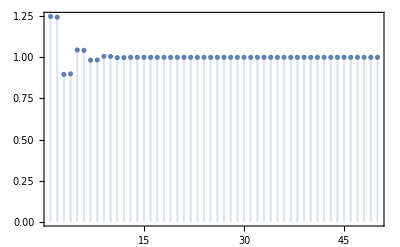

```mathematica
DiscretePlot[doublenotouchpremium[100,90,110,0,0,0.20,1/252,jn],{jn,1,50},Frame->True,PlotRange->{All,{0,Automatic}}]
```

```mathematica
doublenotouchpremium[100,90,110,0,0,0.20,1/4,100]
```

General::munfl: 2.78161×10^-307 7.12807×10^-7 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-765.919] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.417] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.373209

```mathematica
DNT901103m=dntpdesolut[90,110,0,0,0.20,1/4];
```

```mathematica
DNT901103m[100,0]
```

0.373208

```mathematica
Plot3D[doublenotouchpremium[S,90,110,0,0,0.20,1/4-t,100],{S,90,110},{t,0,1/4},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
```

General::munfl: 4.03703×10^-9 2.9256×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-765.864] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.358] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[DNT901103m[S,1/4-t],{S,90,110},{t,0,1/4},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
```

-Graphics3D-

### FX Smile interpolation - mkt

```mathematica
volsfromparam5[atm_,rr25_,st25_,rr10_,st10_]:={atm-rr10/2+st10,atm-rr25/2+st25,atm,atm+rr25/2+st25,atm+rr10/2+st10};
volsfromparam5::"usage"="volsfromparam5[atm,rr25,st25,rr10,st10] returns the vols for {p10d,p25d,atm,c25d,c10d}";
paramfromvols[atm_,c25_,p25_,c10_,p10_]:={atm,c25-p25,(c25+p25)/2-atm,c10-p10,(c10+p10)/2-atm};
paramfromvols::"usage"="paramfromvols[atm,c25,p25,c10,p10] returns the parameters {atm,rr25,st25,rr10,st10}";
volsfrommkt[atm_,rr25_,st25_,rr10_,st10_]:={{atm,atm},{atm+rr25/2+st25,atm-rr25/2+st25},{atm+st25,atm+st25},{atm+rr10/2+st10,atm-rr10/2+st10},{atm+st10,atm+st10}};
volsfrommkt::"usage"="volsfrommkt[atm,rr25,st25,rr10,st10] returns the vols for the traded structures {atm straddle,rr25,st25,rr10,st10}";
volsfromsmlmkt[atm_,rr25_,st25_,rr10_,st10_]:={{atm,atm},{atm+st25,atm+st25},{atm+st10,atm+st10}};
volsfromsmlmkt::"usage"="volsfromsmlmkt[atm,rr25,st25,rr10,st10] returns the vols for the traded structures {atm straddle,st25,st10}";
```

```mathematica
(*
Kfromσδf[f_,σ_,δ_,τ_]:=FindRoot[-(K/f)bsdelta[Sign[δ],1/f,1/K,0,0,σ,τ]==δ,{K,f}]⟦1,2⟧;
Kfromσδf::"usage"="Kfromσδf[f,σ,δ,τ] returns the strike K for a given delta and vol (inverted quote)";
σfromδ[f_,K_,τ_,ϕ_,δ_]:=-ϕ(NNInv[(f δ)/(K ϕ)]+Sqrt[(NNInv[(f δ)/(K ϕ)])^2-2Log[K/f]])/Sqrt[τ];
σfromδ::"usage"="σfromδ[f,K,τ,δ] returns implied vol σ for a given strike and delta (inverted quote)";
*)
Kfromσδf[f_,σ_,δ_,τ_]:=FindRoot[bsdelta[Sign[δ],f,K,0,0,σ,τ]==δ,{K,f}]⟦1,2⟧;
Kfromσδf::"usage"="Kfromσδf[f,σ,δ,τ] returns the strike K for a given delta and vol";
```

```mathematica
Plot3D[Log[Kfromσδf[1,σ,0.25,τ]],{σ,0.05,0.10},{τ,1/252,10},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log[K/f] for 25Δ Call",ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
years=Join[{7,14,21,31,61,92,123,153,184,275,365}/365,{1.5,2,3,4,5,6,7,10}];
```

```mathematica
DateDifference[{2019,8,5},{2020,5,5}]
```

274 days

```mathematica
years2=Join[{7,14,21,31,61,92,122,153,184,274,365}/365,{1.5,2,3,4,5,6,7,10}];
```

```mathematica
volsc25d={0.05297,0.05513,0.05803,0.06095,0.06058,0.061,0.06224,0.063,0.0634,0.06449,0.06672,0.06848,0.06928,0.07319,0.07648,0.07855,0.07993,0.08095,0.08372};
```

```mathematica
volsc25d2={6.19,6.151,5.964,5.979,6.4,6.646,6.615,6.622,6.607,6.715,6.856,7.2,7.388,7.762,8.11,8.368,8.557,8.699,8.965}/100;
```

```mathematica
volsp25d2={6.17,6.154,6.026,6.031,6.51,6.864,6.82,6.82,6.802,6.855,6.944,7.285,7.473,7.842,8.215,8.503,8.705,8.846,9.14}/100;
```

```mathematica
volsatm2={6.02,5.98,5.815,5.81,6.235,6.505,6.463,6.459,6.435,6.505,6.61,6.945,7.13,7.5,7.858,8.128,8.279,8.385,8.665}/100;
```

```mathematica
logkc25d=MapThread[Log[Kfromσδf[1,#1,0.25,#2]]&,{volsc25d,years}];
```

```mathematica
logkc25d2=MapThread[Log[Kfromσδf[1,#1,0.25,#2]]&,{volsc25d2,years2}];
```

```mathematica
logkp25d2=MapThread[Log[Kfromσδf[1,#1,-0.25,#2]]&,{volsp25d2,years2}];
```

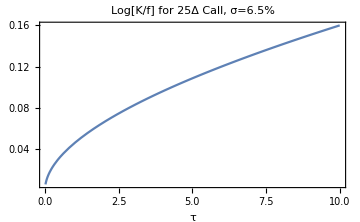

```mathematica
Plot[Log[Kfromσδf[1,0.065,0.25,τ]],{τ,7/365,10},PlotRange->All,PlotLabel->"Log[K/f] for 25Δ Call, σ=6.5%",ImageSize->Medium,Frame->True,FrameLabel->"τ"]
```

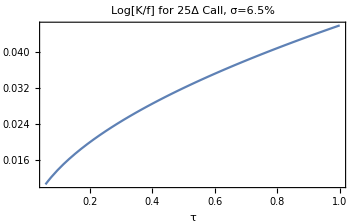

```mathematica
Plot[Log[Kfromσδf[1,0.065,0.25,τ]],{τ,21/365,1},PlotRange->All,PlotLabel->"Log[K/f] for 25Δ Call, σ=6.5%",ImageSize->Medium,Frame->True,FrameLabel->"τ"]
```

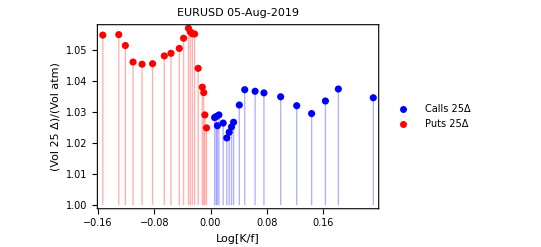

```mathematica
ListPlot[{Transpose[{logkc25d2,volsc25d2/volsatm2}],Transpose[{logkp25d2,volsp25d2/volsatm2}]},Frame->True,PlotRange->All,Filling->Axis,AxesOrigin->{0,1},PlotStyle->{Blue,Red},PlotLegends->{"Calls 25Δ","Puts 25Δ"},PlotLabel->"EURUSD 05-Aug-2019",FrameLabel->{"Log[K/f]","(Vol 25  Δ)/(Vol  atm)"}]
```

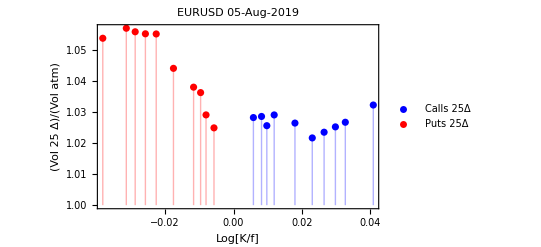

```mathematica
ListPlot[Map[Take[#,10]&,{Transpose[{logkc25d2,volsc25d2/volsatm2}],Transpose[{logkp25d2,volsp25d2/volsatm2}]}],Frame->True,PlotRange->All,Filling->Axis,AxesOrigin->{0,1},PlotStyle->{Blue,Red},PlotLegends->{"Calls 25Δ","Puts 25Δ"},PlotLabel->"EURUSD 05-Aug-2019",FrameLabel->{"Log[K/f]","(Vol 25  Δ)/(Vol  atm)"}]
```

```mathematica
pointsc25d=Transpose[{volsc25d,years,logkc25d}];
```

```mathematica
pointsc25d2=Transpose[{volsc25d2,years2,logkc25d2}];
```

```mathematica
Show[Plot3D[Log[Kfromσδf[1,σ,0.25,τ]],{σ,0.05,0.085},{τ,7/365,10},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log[K/f] for 25Δ Call - 24-May-2021",ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][#3]&)],
ListLinePlot3D[pointsc25d,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Show[Plot3D[Log[Kfromσδf[1,σ,0.25,τ]],{σ,0.05,0.09},{τ,7/365,10},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log[K/f] for 25Δ Call - 05-Aug-2019",ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][#3]&)],
ListLinePlot3D[pointsc25d2,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Show[Plot3D[Log[Kfromσδf[1,σ,0.25,τ]],{σ,0.055,0.075},{τ,7/365,1},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log[K/f] for 25Δ Call - 05-Aug-2019",ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][#3]&)],
ListLinePlot3D[Take[pointsc25d2,11],PlotStyle->Black]]
```

-Graphics3D-

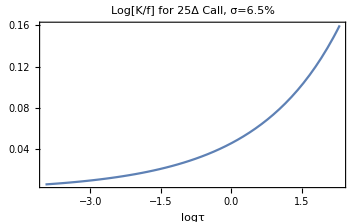

```mathematica
Plot[Log[Kfromσδf[1,0.065,0.25,ⅇ^logτ]],{logτ,Log[7/365],Log[10]},PlotRange->All,PlotLabel->"Log[K/f] for 25Δ Call, σ=6.5%",ImageSize->Medium,Frame->True,FrameLabel->"logτ"]
```

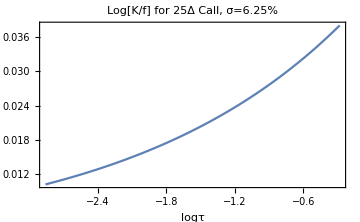

```mathematica
Plot[Log[Kfromσδf[1,0.0625,0.25,ⅇ^logτ]],{logτ,Log[21/365],Log[275/365]},PlotRange->All,PlotLabel->"Log[K/f] for 25Δ Call, σ=6.25%",ImageSize->Medium,Frame->True,FrameLabel->"logτ"]
```

```mathematica
mktstrikesf[atmf_,rr25_,st25_,rr10_,st10_,f_,τ_]:=
Module[{kcstr25d,kpstr25d,kcstr10d,kpstr10d,kcrr25d,kprr25d,kcrr10d,kprr10d},
kcstr25d=Kfromσδf[f,atmf+st25,+0.25,τ];
kpstr25d=Kfromσδf[f,atmf+st25,-0.25,τ];
kcstr10d=Kfromσδf[f,atmf+st10,+0.10,τ];
kpstr10d=Kfromσδf[f,atmf+st10,-0.10,τ];
kcrr25d=Kfromσδf[f,atmf+rr25/2+st25,+0.25,τ];
kprr25d=Kfromσδf[f,atmf-rr25/2+st25,-0.25,τ];
kcrr10d=Kfromσδf[f,atmf+rr10/2+st10,+0.10,τ];
kprr10d=Kfromσδf[f,atmf-rr10/2+st10,-0.10,τ];
{{f,f},{kcrr25d,kprr25d},{kcstr25d,kpstr25d},{kcrr10d,kprr10d},{kcstr10d,kpstr10d}}];
mktstrikesf::"usage"="mktstrikesf[atmf,rr25,st25,rr10,st10,f,τ] returns the strikes for the traded structures {atmf straddle,rr25d,str25d,rr10d,str10d}";

mktstrikesd[atm_,rr25_,st25_,rr10_,st10_,f_,τ_]:=
Module[{kcstr25d,kpstr25d,kcstr10d,kpstr10d,kcrr25d,kprr25d,kcrr10d,kprr10d},
kcstr25d=Kfromσδf[f,atm+st25,+0.25,τ];
kpstr25d=Kfromσδf[f,atm+st25,-0.25,τ];
kcstr10d=Kfromσδf[f,atm+st10,+0.10,τ];
kpstr10d=Kfromσδf[f,atm+st10,-0.10,τ];
kcrr25d=Kfromσδf[f,atm+rr25/2+st25,+0.25,τ];
kprr25d=Kfromσδf[f,atm-rr25/2+st25,-0.25,τ];
kcrr10d=Kfromσδf[f,atm+rr10/2+st10,+0.10,τ];
kprr10d=Kfromσδf[f,atm-rr10/2+st10,-0.10,τ];
{{f ⅇ^((atm^2 τ)/2),f ⅇ^((atm^2 τ)/2)},{kcrr25d,kprr25d},{kcstr25d,kpstr25d},{kcrr10d,kprr10d},{kcstr10d,kpstr10d}}];
mktstrikesf::"usage"="mktstrikesf[atm,rr25,st25,rr10,st10,f,τ] returns the strikes for the traded structures {atm straddle,rr25d,str25d,rr10d,str10d}";

smlmktstrikesf[atm_,rr25_,st25_,rr10_,st10_,f_,τ_]:=
Module[{kcstr25d,kpstr25d,kcstr10d,kpstr10d},
kcstr25d=Kfromσδf[f,atm+st25,+0.25,τ];
kpstr25d=Kfromσδf[f,atm+st25,-0.25,τ];
kcstr10d=Kfromσδf[f,atm+st10,+0.10,τ];
kpstr10d=Kfromσδf[f,atm+st10,-0.10,τ];
{{f,f},{kcstr25d,kpstr25d},{kcstr10d,kpstr10d}}];
smlmktstrikesf::"usage"="smlmktstrikesf[atm,rr25,st25,rr10,st10,f,τ] returns the strikes for the traded structures {atm straddle,str25d,str10d} (inverted quote)";
```

```mathematica
combpremiumf[ls_,{k1_,k2_},{σ1_,σ2_},f_,τ_]:=bspremium[1,f,k1,0,0,σ1,τ]+ls bspremium[-1,f,k2,0,0,σ2,τ];
combpremiumf::"usage"="combpremiumf[ls,{k1,k2},{σ1,σ2},f,τ] returns the premium for a traded structure {atm straddle,rr25d,str25d,rr10d,str10d} (inverted quote)";
stratpremiaf[strats_,strikes_,vols_,f_,τ_]:=MapThread[combpremiumf[#1,#2,#3,f,τ]&,{strats,strikes,vols}];
stratpremiaf::"usage"="stratpremiaf[strats,strikes,vols,f,τ] returns the premia for the traded structures {atm straddle,rr25d,str25d,rr10d,str10d} (inverted quote)";
```

```mathematica
volsfromparam5[0.05877, 0.00148, 0.00144,0.00257,0.00430]
```

{0.061785,0.05947,0.05877,0.06095,0.064355}

```mathematica
volsfrommkt[0.05877, 0.00148, 0.00144,0.00257,0.00430]
```

{{0.05877,0.05877},{0.06095,0.05947},{0.06021,0.06021},{0.064355,0.061785},{0.06307,0.06307}}

```mathematica
mktstrikesd[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365]
```

{{1.22248,1.22248},{1.23723,1.20828},{1.23704,1.2081},{1.25225,1.19461},{1.25165,1.19405}}

```mathematica
stratpremiaf[{1,-1,1,-1,1},
mktstrikesd[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365],
volsfrommkt[0.05877, 0.00148, 0.00144,0.00257,0.00430],1.2223,31/365]
```

{0.0167052,0.0000224137,0.00639846,0.0000271008,0.00212738}

```mathematica
stratpremiaf[{1,-1,1,-1,1},
mktstrikesd[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365],
volsfrommkt[0.05877, 0.00148, 0.00144,0.00257,0.00430],1.2223,31/365]*10^6
```

{16705.2,22.4137,6398.46,27.1008,2127.38}

```mathematica
volsfrommkt[0.216215, -0.005, 0.007375,0,0]
```

{{0.216215,0.216215},{0.22109,0.22609},{0.22359,0.22359},{0.216215,0.216215},{0.216215,0.216215}}

```mathematica
mktstrikesd[0.216215, -0.005, 0.007375,0,0,1.3070,0.0849]
```

{{1.3096,1.3096},{1.36788,1.25291},{1.36861,1.25347},{1.41972,1.20802},{1.41972,1.20802}}

```mathematica
Kλ[u_,λ_]:=ⅇ^(-1/2(u/λ)^2);
```

```mathematica
Nxs[x_,xs_]:=Map[Abs[x-#]&,xs];
```

```mathematica
Ksλ[x_,λ_,xs_,nk_]:=Map[Kλ[#,λ]&,Nxs[x,xs]];
```

```mathematica
Φλ[x_,λ_,xs_,nk_]:=Total[Map[Kλ[#,λ]&,Nxs[x,xs]]];
```

```mathematica
g[x_,λ_,αs_,xs_,nk_]:=Dot[αs,Ksλ[x,λ,xs,nk]]/Φλ[x,λ,xs,nk];
```

```mathematica
extrapolate[anchors_,vols_]:=Module[{dac,dap,dvc,dvp},
dac=2anchors[[4]]-anchors[[2]];
dap=2anchors[[5]]-anchors[[3]];
dvc=2vols[[4]]-vols[[2]];
dvp=2vols[[5]]-vols[[3]];
{Join[anchors,{dac,dap}],Join[vols,{dvc,dvp}]}];
```

```mathematica
extrapolateslope[anchors_,vols_]:=Module[{dac,dap,dvc,dvp},
dac=anchors[[4]]-anchors[[2]];
dap=anchors[[5]]-anchors[[3]];
dvc=vols[[4]]-vols[[2]];
dvp=vols[[5]]-vols[[3]];
{dvc/dac,dvp/dap}];
```

```mathematica
gtail[x_,λ_,αs_,xs_,nk_,sc_,sp_]:=Module[{xp,σp,xc,σc},
xp=Min[xs];σp=g[xp,λ,αs,xs,nk];
xc=Max[xs];σc=g[xc,λ,αs,xs,nk];
Piecewise[{{σc+( x-xc)sc, x>xc}, {σp+ (x-xp)sp, x< xp}, {g[x,λ,αs,xs,nk], True}}]];
```

```mathematica
interpolvol[atm_,rr25_,st25_,rr10_,st10_,f_,τ_]:=Module[
{volspairs,strikespairs,stratssigns,stratsleg1,stratsleg2,stratslegs,
premiapairs,logks,λ,
npts,anchors,vols,sol,αsol,
(*npts7,anchors7,vols7,sol7,αsol7,*)
(*args,diffs,*)
eqatm,eqrr25,eqrr10,eqst25,eqst10,
soleq,αsoleq,soleqvols,
sp,sc,
deltas,λδ,solδ,αsolδ},

volspairs=volsfrommkt[atm,rr25,st25,rr10,st10];
strikespairs=mktstrikesd[atm,rr25,st25,rr10,st10,f,τ];
(*stratssigns=Transpose[{{1,1,1,1,1},{-1,-1,-1,-1,-1}}];
stratsleg1={1,1,1,1,1};
stratsleg2={1,-1,1,-1,1};
premiapairs=stratpremiaf[stratsleg2,strikespairs,volspairs,f,τ];
stratslegs=Transpose[{stratsleg1,stratsleg2}];*)
logks=Log[strikespairs/f];
npts=5;
anchors={logks⟦1,1⟧,logks⟦2,1⟧,logks⟦2,2⟧,logks⟦4,1⟧,logks⟦4,2⟧};
vols={volspairs⟦1,1⟧,volspairs⟦2,1⟧,volspairs⟦2,2⟧,volspairs⟦4,1⟧,volspairs⟦4,2⟧};
λ=(logks⟦2,1⟧-logks⟦2,2⟧)/2;

sol=First[Solve[MapThread[g[#1,λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]==#2&,{anchors,vols}],
Table[Subscript[α, j],{j,1,npts}]]];
αsol=Map[Last,sol];

eqatm=g[(atm^2 τ)/2,λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-atm;
eqrr25=g[anchors[[2]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-
g[anchors[[3]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-rr25;
eqrr10=g[anchors[[4]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-
g[anchors[[5]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-rr10;
eqst25=(bspremium[1,f,strikespairs[[3,1]],0,0,g[logks[[3,1]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts],τ]+
bspremium[-1,f,strikespairs[[3,2]],0,0,g[logks[[3,2]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts],τ])-(
bspremium[1,f,strikespairs[[3,1]],0,0,volspairs[[3,1]],τ]+
bspremium[-1,f,strikespairs[[3,2]],0,0,volspairs[[3,2]],τ]);
eqst10=(bspremium[1,f,strikespairs[[5,1]],0,0,g[logks[[5,1]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts],τ]+
bspremium[-1,f,strikespairs[[5,2]],0,0,g[logks[[5,2]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts],τ])-(
bspremium[1,f,strikespairs[[5,1]],0,0,volspairs[[5,1]],τ]+
bspremium[-1,f,strikespairs[[5,2]],0,0,volspairs[[5,2]],τ]);
soleq=FindRoot[{eqatm,eqrr25,eqrr10,eqst25,eqst10},Transpose[{Table[Subscript[α, j],{j,1,npts}],αsol}]];
αsoleq=Map[Last,soleq];

soleqvols=Map[g[#,λ,αsoleq,anchors,npts]&,anchors];
{sc,sp}=extrapolateslope[anchors,soleqvols];

(* diffs=MapThread[{Dot[#1,#2],#3}&,{stratslegs,Map[Apply[bspremium,#]&,args/.sol2,{2}],premiapairs}]; *)
deltas={0.50,0.25,0.75,0.10,0.90};
λδ=0.25;
solδ=First[Solve[MapThread[g[#1,λδ,Table[Subscript[α, j],{j,1,npts}],deltas,npts]==#2&,{deltas,vols}]]];
αsolδ=Map[Last,solδ];
{anchors,vols,deltas,{λ,λδ},αsoleq,soleqvols,αsolδ,{sc,sp}}
];
```

```mathematica
Grid[interpolvol[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365]]
```

0.000146673 | 0.0121385 | -0.0115396 | 0.0242114 | -0.0229135
0.05877 | 0.06095 | 0.05947 | 0.064355 | 0.061785
0.5 | 0.25 | 0.75 | 0.1 | 0.9
0.0118391 | 0.25 |  |  | 
0.0576963 | 0.0589605 | 0.0566463 | 0.068479 | 0.0656629
0.05877 | 0.0609566 | 0.0594766 | 0.0643508 | 0.0617808
0.0788643 | 0.0272054 | 0.0299293 | 0.0924017 | 0.0846388
0.281148 | -0.202592 |  |  |

```mathematica
interpolvol[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365]
```

{{0.000146673,0.0121385,-0.0115396,0.0242114,-0.0229135},{0.05877,0.06095,0.05947,0.064355,0.061785},{0.5,0.25,0.75,0.1,0.9},{0.0118391,0.25},{0.0576963,0.0589605,0.0566463,0.068479,0.0656629},{0.05877,0.0609566,0.0594766,0.0643508,0.0617808},{0.0788643,0.0272054,0.0299293,0.0924017,0.0846388},{0.281148,-0.202592}}

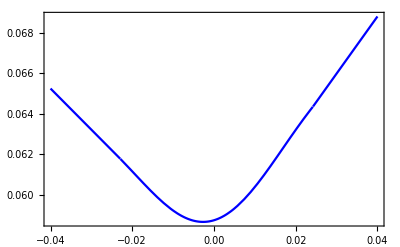

```mathematica
Plot[{
gtail[x,0.011839060322642678,{0.05769632193039086,0.05896050785540159,0.05664627516711007,0.06847902756025366,0.06566292829571305},{0.00014667301356155048,0.01213849159743891,-0.011539629047846446,0.02421135445649408,-0.022913520990713924},5,0.28114805595095743,-0.20259221154557136]},{x,-0.04,+0.04},PlotStyle->{Blue},Frame->True,PlotRange->All]
```

```mathematica
showplots[atm_,rr25_,st25_,rr10_,st10_,f_,τ_,title_,ζ_:3,size_:300]:=Module[{npts,anchors,vols,deltas,λ,λδ,αsoleq,soleqvols,αsolδ,sc,sp,xmin,xmax},
npts=5;
{anchors,vols,deltas,{λ,λδ},αsoleq,soleqvols,αsolδ,{sc,sp}}=interpolvol[atm,rr25,st25,rr10,st10,f,τ];
Print[Grid[{anchors,αsoleq,soleqvols,αsolδ,{sc,sp}}]];
xmin=ζ Min[anchors];xmax=ζ Max[anchors];
Grid[{{
(*First Chart*)
Show[
(*Plot σ(logK) with logstrike interpolation and extrapolation*)
Plot[gtail[x,λ,αsoleq,anchors,npts,sc,sp],{x,xmin,xmax},Frame->True,PlotStyle->{Darker[Green]},ImageSize->size,FrameLabel->{"Log[K/f]","σ"},PlotLabel->StringJoin[title," , LogStrike, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(logK) with logstrike interpolation*)
Plot[g[x,λ,αsoleq,anchors,npts],{x,xmin,xmax},Frame->True,PlotStyle->{Blue},ImageSize->size,FrameLabel->{"Log[K/f]","σ"},PlotLabel->StringJoin[title," , LogStrike, λ=",ToString[Round[λ,0.001]]]],
(*Plot points*)
ListPlot[Transpose[{anchors,vols}],Frame->True,PlotStyle->{PointSize[0.02],Red},PlotRange->All]
],
(*Second Chart*)
Show[
(*Plot σ(Δ) with logstrike interpolation and extrapolation*)
ParametricPlot[{bsdelta[1,f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],gtail[x,λ,αsoleq,anchors,npts,sc,sp]},
{x,xmin,xmax},Frame->True,PlotStyle->{Darker[Green]},AspectRatio->2/3,AxesOrigin->{0.5,atm},ImageSize->size,FrameLabel->{"Δ_c","σ"},PlotLabel->StringJoin[title," , Delta, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) with logstrike interpolation*)
ParametricPlot[{bsdelta[1,f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],g[x,λ,αsoleq,anchors,npts]},
{x,xmin,xmax},Frame->True,PlotStyle->{Blue},AspectRatio->2/3,AxesOrigin->{0.5,atm},ImageSize->size,FrameLabel->{"Δ_c","σ"},PlotLabel->StringJoin[title," , Delta, λ=",ToString[Round[λ,0.001]]]],
(*Plot points*)
ListPlot[Transpose[{{0.50,0.25,0.75,0.10,0.90},vols}],Frame->True,PlotStyle->{PointSize[0.02],Red}],
(*Plot σ(Δ) with Δ interpolation and extrapolation*)
Plot[g[x,λδ,αsolδ,deltas,npts],{x,0,1},Frame->True,PlotStyle->Gray,PlotRange->All]
],
(*Third Chart*)
Show[
(*Plot Premium(logk) puts from logstrike interpolation*)
Plot[bspremium[Sign[x],f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],
{x,xmin,Min[anchors]},Frame->True,PlotStyle->{Blue},AspectRatio->3/4,AxesOrigin->{0,0},ImageSize->size,FrameLabel->{"Log[K/f]","Premium"},PlotRange->All,PlotLabel->StringJoin[title," , Premium, λ=",ToString[Round[λ,0.001]]]],
(*Plot Premium(logk) calls from logstrike interpolation*)
Plot[bspremium[Sign[x],f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],
{x,Max[anchors],xmax},Frame->True,PlotStyle->{Blue},AspectRatio->3/4,AxesOrigin->{0,0},ImageSize->size,FrameLabel->{"Log[K/f]","Premium"},PlotRange->All,PlotLabel->StringJoin[title," , Premium, λ=",ToString[Round[λ,0.001]]]],
(*Plot Premium(logk) puts from logstrike interpolation and extrapolation*)
Plot[bspremium[Sign[x],f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],
{x,xmin,Min[anchors]},Frame->True,PlotStyle->{Darker[Green]},AspectRatio->3/4,AxesOrigin->{0,0},ImageSize->size,FrameLabel->{"Log[K/f]","Premium"},PlotRange->All,PlotLabel->StringJoin[title," , Premium, λ=",ToString[Round[λ,0.001]]]],
(*Plot Premium(logk) calls from logstrike interpolation and extrapolation*)
Plot[bspremium[Sign[x],f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],
{x,Max[anchors],xmax},Frame->True,PlotStyle->{Darker[Green]},AspectRatio->3/4,AxesOrigin->{0,0},ImageSize->size,FrameLabel->{"Log[K/f]","Premium"},PlotRange->All,PlotLabel->StringJoin[title," , Premium, λ=",ToString[Round[λ,0.001]]]]
],
(*Fourth Chart*)
Show[
(*Plot σ(Δ) puts from logstrike interpolation and extrapolation*)
ParametricPlot[{-bsdelta[Sign[x],f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],gtail[x,λ,αsoleq,anchors,npts,sc,sp]},
{x,xmin,Min[anchors]},Frame->True,PlotStyle->{Darker[Green]},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) calls from logstrike interpolation and extrapolation*)
ParametricPlot[{bsdelta[Sign[x],f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],gtail[x,λ,αsoleq,anchors,npts,sc,sp]},
{x,Max[anchors],xmax},Frame->True,PlotStyle->{Dashed,Darker[Green]},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) puts from logstrike interpolation*)
ParametricPlot[{-bsdelta[Sign[x],f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],g[x,λ,αsoleq,anchors,npts]},
{x,xmin,Min[anchors]},Frame->True,PlotStyle->{Blue},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) calls from logstrike interpolation*)
ParametricPlot[{bsdelta[Sign[x],f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],g[x,λ,αsoleq,anchors,npts]},
{x,Max[anchors],xmax},Frame->True,PlotStyle->{Dashed,Blue},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) puts from Δ interpolation*)
ParametricPlot[{1-x,g[x,λδ,αsolδ,deltas,npts]},
{x,0.875,1},Frame->True,PlotStyle->{Gray},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) calls from Δ interpolation*)
ParametricPlot[{x,g[x,λδ,αsolδ,deltas,npts]},
{x,0,0.125},Frame->True,PlotStyle->{Dashed,Gray},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]]]
}}]]
```

#### FX Smile interpolation - SVI

```mathematica
varSVI[k_,a_,b_,σ_,ρ_,m_]:=a+b(ρ(k-m)+Sqrt[(k-m)^2+σ^2]);
varSVI::"usage"="varSVI[k,a,b,σ,ρ,m] returns the SVI variance given the parameters a,b,σ,ρ,m and the logstrike k = Log[K/F]";
volSVI[k_,a_,b_,σ_,ρ_,m_]:=Sqrt[a+b(ρ(k-m)+Sqrt[(k-m)^2+σ^2])];
volSVI::"usage"="volSVI[k,a,b,σ,ρ,m] returns the SVI volatility given the parameters a,b,σ,ρ,m and the logstrike k = Log[K/F]";
```

```mathematica
interpolvol[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365]
```

{{0.000146673,0.0121385,-0.0115396,0.0242114,-0.0229135},{0.05877,0.06095,0.05947,0.064355,0.061785},{0.5,0.25,0.75,0.1,0.9},{0.0118391,0.25},{0.0576963,0.0589605,0.0566463,0.068479,0.0656629},{0.05877,0.0609566,0.0594766,0.0643508,0.0617808},{0.0788643,0.0272054,0.0299293,0.0924017,0.0846388},{0.281148,-0.202592}}

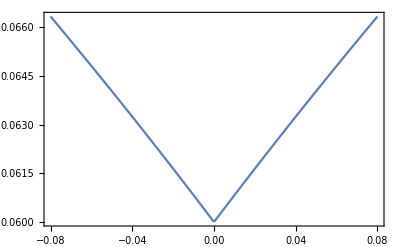

```mathematica
Plot[volSVI[k,0.06^2,0.01,0,0,0],{k,-0.08,+0.08},Frame->True,PlotRange->All]
```

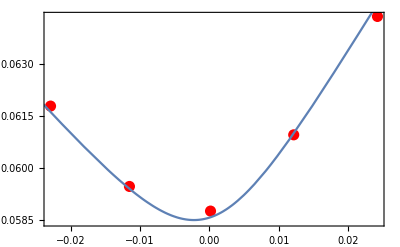

```mathematica
Show[ListPlot[Transpose[{{0.00014667301356155048,0.01213849159743891,-0.011539629047846446,0.02421135445649408,-0.022913520990713924},{0.058770000000000024,0.06095655405998937,0.05947655405998937,0.06435081598257525,0.061780815982575246}}],PlotRange->All,PlotStyle->{PointSize[0.02],Red},Frame->True]
,Plot[volSVI[k,(0.055)^2,0.037,0.011,0.2,0],{k,-0.08,+0.08},Frame->True,PlotRange->All]]
```

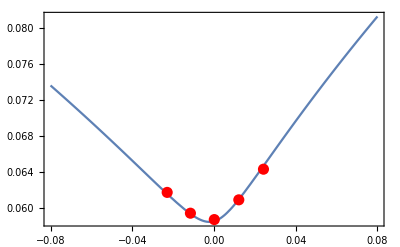

```mathematica
Show[Plot[volSVI[k,(0.055)^2,0.037,0.011,0.2,0],{k,-0.08,+0.08},Frame->True,PlotRange->All],ListPlot[Transpose[{{0.00014667301356155048,0.01213849159743891,-0.011539629047846446,0.02421135445649408,-0.022913520990713924},{0.058770000000000024,0.06095655405998937,0.05947655405998937,0.06435081598257525,0.061780815982575246}}],PlotRange->All,PlotStyle->{PointSize[0.02],Red},Frame->True]
]
```

0.000146673 | 0.0121385 | -0.0115396 | 0.0242114 | -0.0229135
0.0576963 | 0.0589605 | 0.0566463 | 0.068479 | 0.0656629
0.05877 | 0.0609566 | 0.0594766 | 0.0643508 | 0.0617808
0.0788643 | 0.0272054 | 0.0299293 | 0.0924017 | 0.0846388
0.281148 | -0.202592 |  |  |

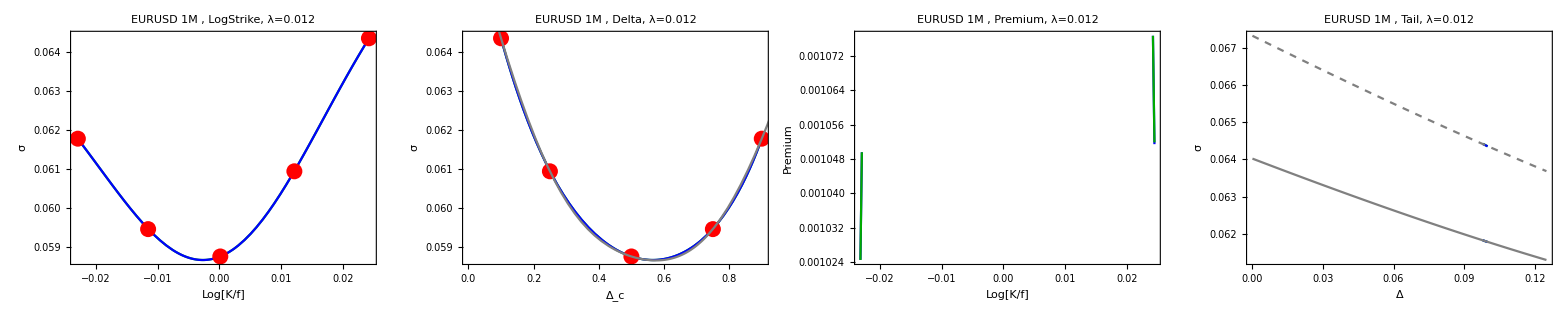

```mathematica
showplots[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365,"EURUSD 1M",1.01,Large]
```

0.000146673 | 0.0121385 | -0.0115396 | 0.0242114 | -0.0229135
0.0576963 | 0.0589605 | 0.0566463 | 0.068479 | 0.0656629
0.05877 | 0.0609566 | 0.0594766 | 0.0643508 | 0.0617808
0.0788643 | 0.0272054 | 0.0299293 | 0.0924017 | 0.0846388
0.281148 | -0.202592 |  |  |

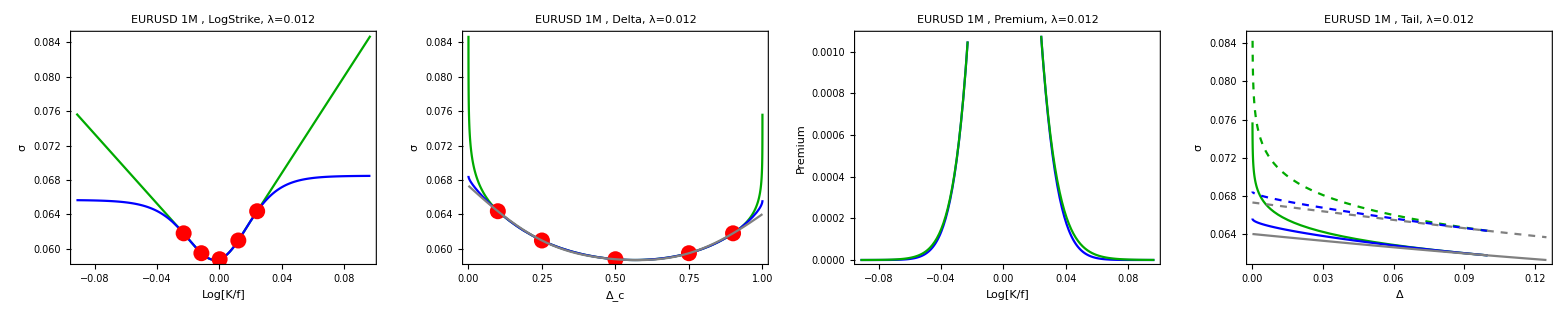

```mathematica
showplots[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365,"EURUSD 1M",4,Large]
```

0.000429677 | 0.0211253 | -0.0197346 | 0.0428123 | -0.040188
0.0575259 | 0.0580126 | 0.0554005 | 0.0711073 | 0.0688409
0.05839 | 0.0610067 | 0.0596067 | 0.0656922 | 0.0632422
0.0910503 | 0.00941381 | 0.0121405 | 0.107275 | 0.0997698
0.216049 | -0.177744 |  |  |

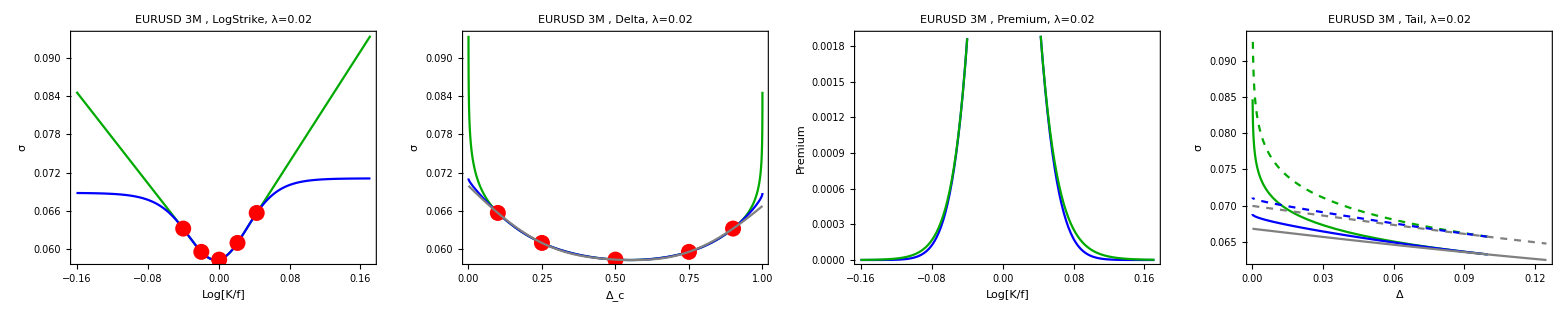

```mathematica
showplots[0.05839, 0.00140, 0.00191,0.00245,0.00608,1.2238,92/365,"EURUSD 3M",4,Large]
```

0.000913457 | 0.03138 | -0.0288164 | 0.0646169 | -0.0603318
0.0580024 | 0.0604607 | 0.0578531 | 0.0760113 | 0.0744593
0.0602 | 0.0634162 | 0.0622162 | 0.0696694 | 0.0675694
0.106613 | -0.00827217 | -0.00593499 | 0.126773 | 0.12034
0.188141 | -0.16986 |  |  |

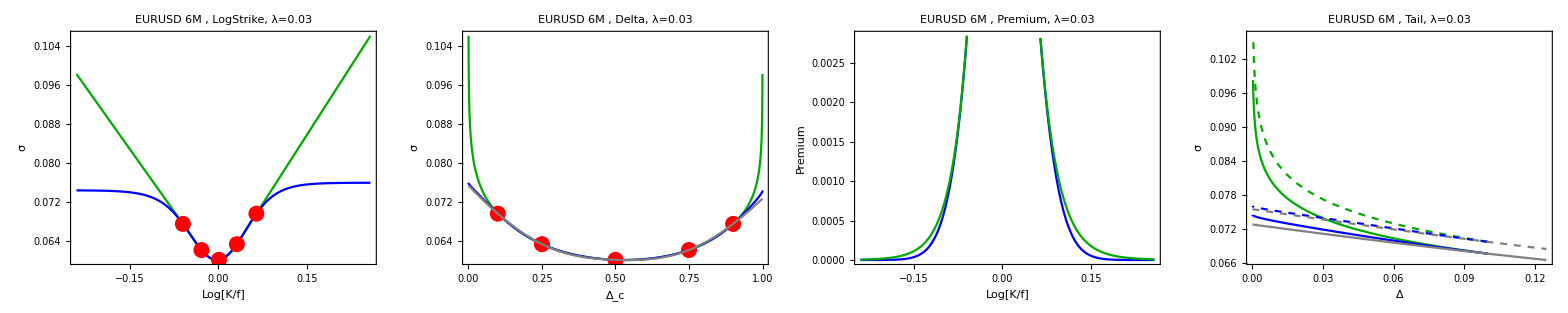

```mathematica
showplots[0.06020, 0.00120, 0.00261,0.00210,0.00842,1.2260,184/365,"EURUSD 6M",4,Large]
```

0.00207304 | 0.047224 | -0.0440775 | 0.0979456 | -0.0973101
0.0620927 | 0.0609942 | 0.0648215 | 0.0828053 | 0.0867513
0.06439 | 0.0667157 | 0.0688657 | 0.0742449 | 0.0782949
0.139871 | -0.0389341 | -0.0454017 | 0.154111 | 0.168098
0.148441 | -0.177132 |  |  |

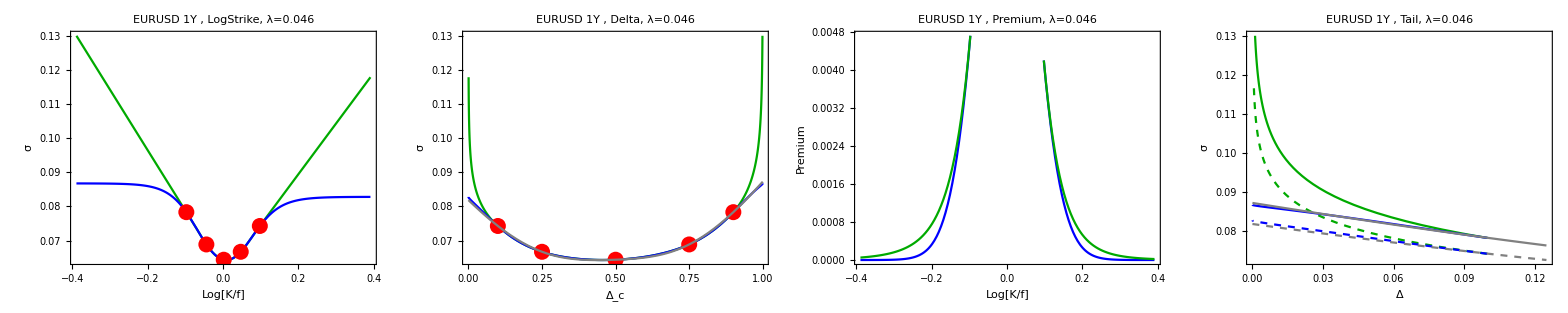

```mathematica
showplots[0.06439, -0.00215, 0.00340,-0.00405,0.01191,1.2308,365/365,"EURUSD 1Y",4,Large]
```

C[K_2]=((K_2-S_0)/(K_1-S_0))^(1-α)C[K_1]

```mathematica
With[{α=2.5,S0=1,δ=0.1,σ1=0.145,τ=1/4},K1=S0(1+δ);bsdelta[1,S0,K1,0,0,σ1,τ]]
```

0.100559

```mathematica
With[{α=3.5,S0=1,δ=0.1,σ1=0.145,τ=1/4},
K1=S0(1+δ);
Plot3D[{((K2-S0)/(K1-S0))^(1-α)},{K2,K1,K1(1+δ)^2},{σ2,σ1,3σ1},PlotRange->All,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]]
```

-Graphics3D-

```mathematica
σK[K1_,K2_,σ1_,δσ_]:=σ1+Log[K2/K1]δσ;
```

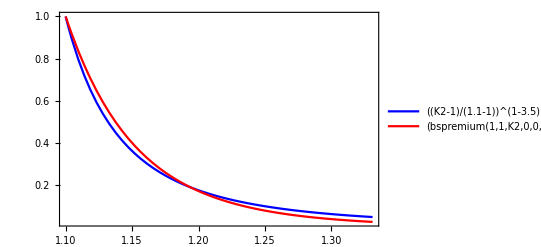

```mathematica
With[{α=3.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/3.2},
Plot[{((K2-S0)/(K1-S0))^(1-α),(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ])},{K2,K1,K1(1+δ)^2},
PlotRange->All,Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red}]]
```

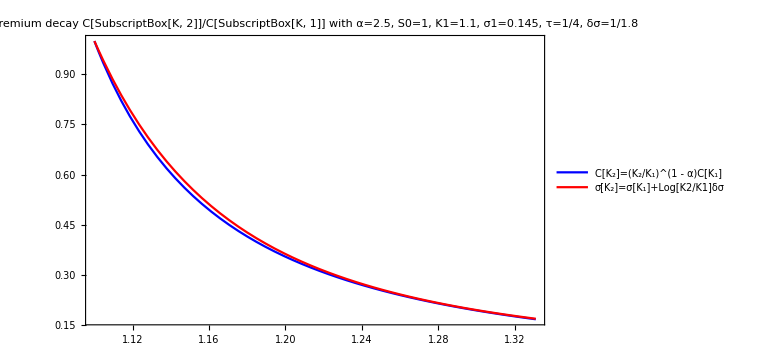

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
Plot[{((K2-S0)/(K1-S0))^(1-α),(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ])},{K2,K1,K1(1+δ)^2},
PlotRange->All,Frame->True,PlotLegends->{"C[K_2]=(K_2/K_1)^(1 - α)C[K_1]","σ[K_2]=σ[K_1]+Log[K2/K1]δσ"},
PlotStyle->{Blue,Red},ImageSize->Large,PlotLabel->"Premium decay C[SubscriptBox[K, 2]]/C[SubscriptBox[K, 1]] with α=2.5, S0=1, K1=1.1, σ1=0.145, τ=1/4, δσ=1/1.8"]]
```

```mathematica
Refine[bsdelta[1,f,K,0,0,σ,τ],τ>0&&f≠K]
```

1/2 Erfc[-((σ^2 τ)/2+Log[f/K])/(√2 σ √τ)]

((σ^2 τ)/2+Log[f/K])/(√2 σ √τ)==-InverseErfc[2δ]

((σ √τ)^2/2+Log[f/K])/(σ √τ)==-√2InverseErfc[2δ]

1/2 σ √τ+Log[f/K]/(σ √τ)==-√2InverseErfc[2δ]

Log[f/K]/(σ √τ)==-√2InverseErfc[2δ]-1/2 σ √τ

Log[f/K]==-σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ)

Log[K/f]==σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ)

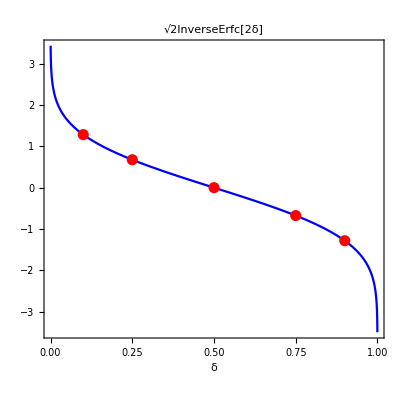

```mathematica
Show[Plot[√2 InverseErfc[2δ],{δ,0,1},AspectRatio->1,Frame->True,PlotStyle->Blue,AxesOrigin->{1/2,0},FrameLabel->{"δ"},PlotLabel->"√2InverseErfc[2δ]"],
ListPlot[Map[{#,√2 InverseErfc[2#]}&,{0.50,0.25,0.75,0.10,0.90}],AspectRatio->1,Frame->True,PlotStyle->{PointSize[0.02],Red},AxesOrigin->{1/2,0}]]
```

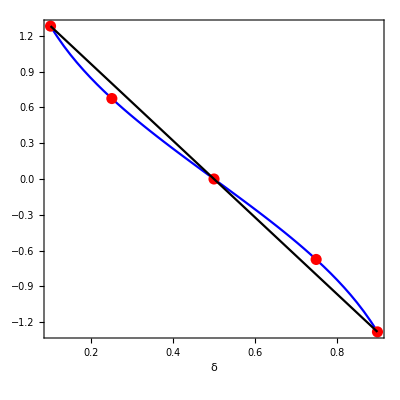

```mathematica
Show[Plot[√2 InverseErfc[2δ],{δ,0.1,1-0.1},AspectRatio->1,Frame->True,PlotStyle->Blue,AxesOrigin->{1/2,0},FrameLabel->{"δ"}],
ListPlot[Map[{#,√2 InverseErfc[2#]}&,{0.50,0.25,0.75,0.10,0.90}],AspectRatio->1,Frame->True,PlotStyle->{PointSize[0.02],Red},AxesOrigin->{1/2,0}],
ListLinePlot[Map[{#,√2 InverseErfc[2#]}&,{0.10,0.90}],AspectRatio->1,Frame->True,PlotStyle->{Black},AxesOrigin->{1/2,0}]]
```

```mathematica
σMalz[atm_,rr25_,st25_,δ_]:=atm-2rr25(δ-1/2)+16st25(δ-1/2)^2;
```

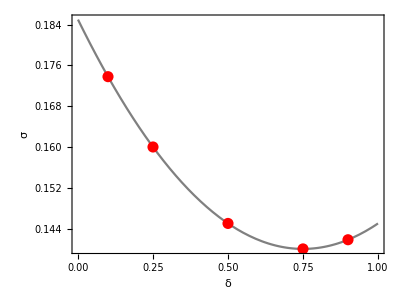

```mathematica
With[{atm=0.145,rr25=0.02,st25=0.005},Show[Plot[σMalz[atm,rr25,st25,δ],{δ,0,1},AspectRatio->3/4,Frame->True,PlotStyle->Gray,AxesOrigin->{1/2,atm},FrameLabel->{"δ","σ"}],
ListPlot[Map[{#,σMalz[atm,rr25,st25,#]}&,{0.50,0.25,0.75,0.10,0.90}],AspectRatio->3/4,Frame->True,PlotStyle->{PointSize[0.02],Red},AxesOrigin->{1/2,atm}]]]
```

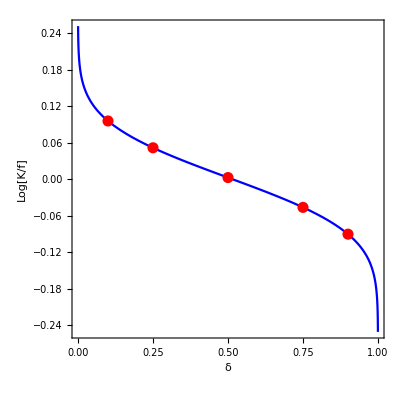

```mathematica
With[{σ=0.145,τ=1/4},Show[Plot[σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ),{δ,0,1},AspectRatio->1,Frame->True,PlotStyle->Blue,AxesOrigin->{1/2,0},FrameLabel->{"δ","Log[K/f]"}],
ListPlot[Map[{#,σ √τ(√2 InverseErfc[2#]+1/2 σ √τ)}&,{0.50,0.25,0.75,0.10,0.90}],AspectRatio->1,Frame->True,PlotStyle->{PointSize[0.02],Red},AxesOrigin->{1/2,0}]]]
```

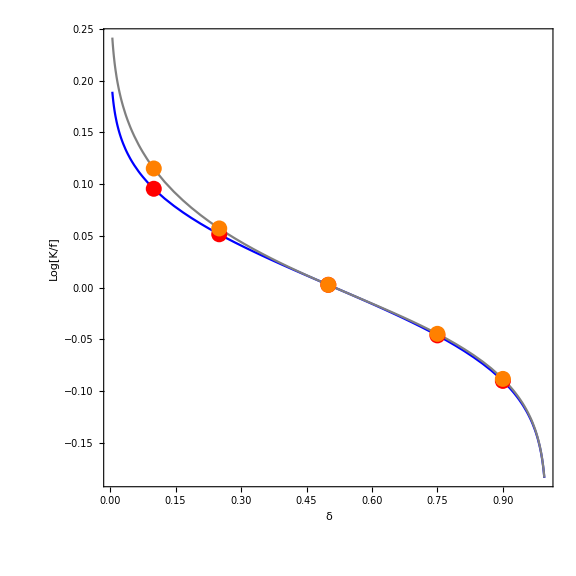

```mathematica
With[{σ=0.145,atm=0.145,rr25=0.02,st25=0.005,τ=1/4},Show[Plot[{
σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ),
σMalz[atm,rr25,st25,δ] √τ(√2 InverseErfc[2δ]+1/2 σMalz[atm,rr25,st25,δ] √τ)},
{δ,0.005,1-0.005},AspectRatio->1,Frame->True,PlotStyle->{Blue,Gray},
AxesOrigin->{1/2,0},FrameLabel->{"δ","Log[K/f]"},PlotRange->All,ImageSize->Large],
ListPlot[{Map[{#,σ √τ(√2 InverseErfc[2#]+1/2 σ √τ)}&,{0.50,0.25,0.75,0.10,0.90}],
Map[{#,σMalz[atm,rr25,st25,#] √τ(√2 InverseErfc[2#]+1/2 σMalz[atm,rr25,st25,#] √τ)}&,{0.50,0.25,0.75,0.10,0.90}]},
AspectRatio->1,Frame->True,PlotStyle->{{PointSize[0.02],Red},{PointSize[0.02],Orange}},AxesOrigin->{1/2,0}]]]
```

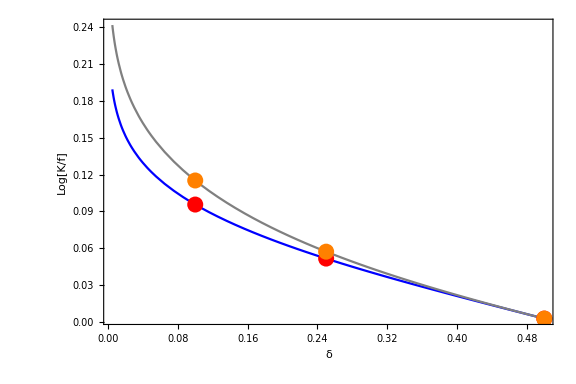

```mathematica
With[{σ=0.145,atm=0.145,rr25=0.02,st25=0.005,τ=1/4},Show[Plot[{
σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ),
σMalz[atm,rr25,st25,δ] √τ(√2 InverseErfc[2δ]+1/2 σMalz[atm,rr25,st25,δ] √τ)},
{δ,0.005,0.5},AspectRatio->2/3,Frame->True,PlotStyle->{Blue,Gray},
AxesOrigin->{1/2,0},FrameLabel->{"δ","Log[K/f]"},PlotRange->All,ImageSize->Large],
ListPlot[{Map[{#,σ √τ(√2 InverseErfc[2#]+1/2 σ √τ)}&,{0.50,0.25,0.10}],
Map[{#,σMalz[atm,rr25,st25,#] √τ(√2 InverseErfc[2#]+1/2 σMalz[atm,rr25,st25,#] √τ)}&,{0.50,0.25,0.10}]},
AspectRatio->1,Frame->True,PlotStyle->{{PointSize[0.02],Red},{PointSize[0.02],Orange}},AxesOrigin->{1/2,0}]]]
```

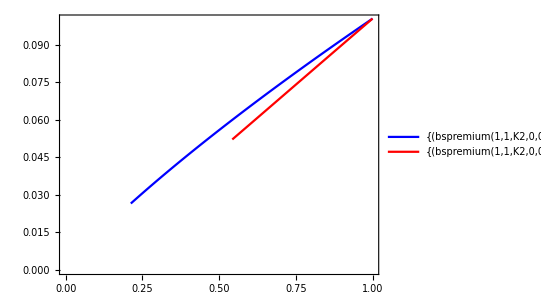

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
ParametricPlot[{{(bspremium[1,S0,K2,0,0,σ1,τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σ1,τ]},
{(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]}},
{K2,K1,K1(1+δ)^0.5},
PlotRange->{{0,1},{0,0.10}},Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red},AspectRatio->3/4]]
```

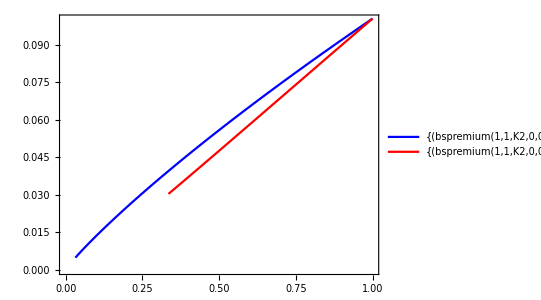

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
ParametricPlot[{{(bspremium[1,S0,K2,0,0,σ1,τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σ1,τ]},
{(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]}},
{K2,K1,K1(1+δ)^1},
PlotRange->{{0,1},{0,0.10}},Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red},AspectRatio->3/4]]
```

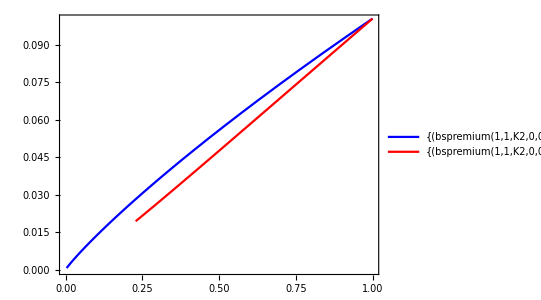

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
ParametricPlot[{{(bspremium[1,S0,K2,0,0,σ1,τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σ1,τ]},
{(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]}},
{K2,K1,K1(1+δ)^1.5},
PlotRange->{{0,1},{0,0.10}},Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red},AspectRatio->3/4]]
```

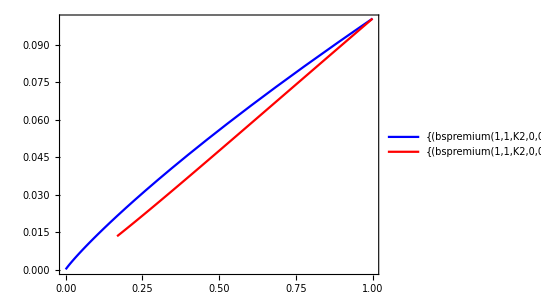

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
ParametricPlot[{{(bspremium[1,S0,K2,0,0,σ1,τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σ1,τ]},
{(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]}},
{K2,K1,K1(1+δ)^2},
PlotRange->{{0,1},{0,0.10}},Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red},AspectRatio->3/4]]
```